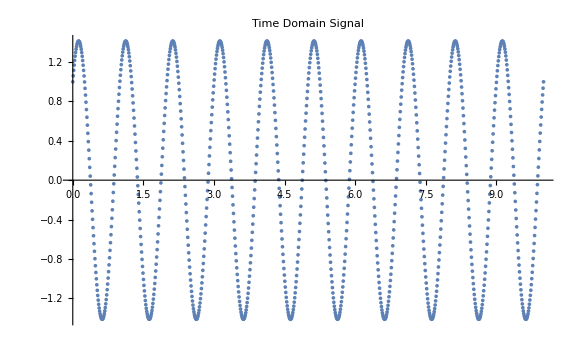
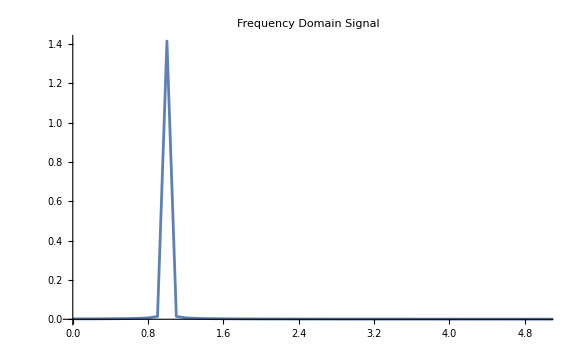

```mathematica
ClearAll["Global`*"];
T=1.;
n=1000;
span=10*T;
data=Table[{t,Sin[t*2 π/T]+Cos[t*2 π/T]},{t,Subdivide[0,span,n-1]}];

(*Calculate the FFT magnitude without any additional normalization*)
fft=2*Abs@Fourier[data[[;;-1,2]],FourierParameters->{-1, 1}];

(*Calculate the frequency bins*)
Fs=n/span;
freq=Table[i*Fs/n,{i,0,n/2-1}]; (*Positive frequencies*)

{ListPlot[data,ImageSize->Large,PlotLabel->"Time Domain Signal"],ListPlot[Transpose[{freq,fft[[;;n/2]]}],Joined->True,PlotRange->{{0,5},All},ImageSize->Large,PlotLabel->"Frequency Domain Signal"]}
```

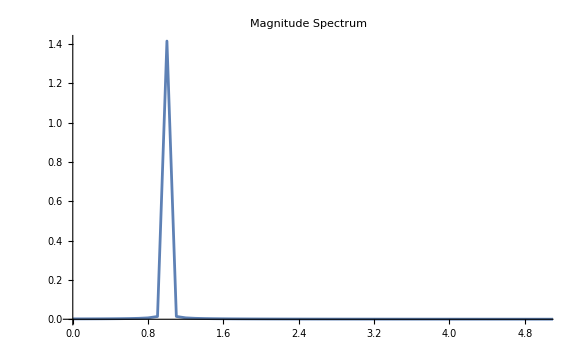
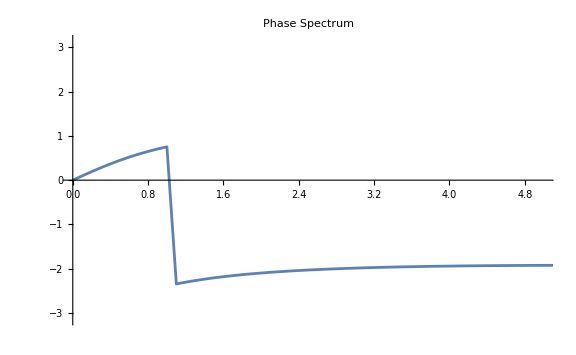
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Calculate the FFT magnitude and phase without any additional normalization*)
fftMagnitude=2*Abs@Fourier[data[[;;-1,2]],FourierParameters->{-1,1}];
fftPhase=Arg@Fourier[data[[;;-1,2]],FourierParameters->{-1,1}];

(*Calculate the frequency bins*)
Fs=n/span;
freq=Table[i*Fs/n,{i,0,n/2-1}]; (*Positive frequencies*)

{ListPlot[data,ImageSize->Large,PlotLabel->"Time Domain Signal"],ListPlot[Transpose[{freq,fftMagnitude[[;;n/2]]}],Joined->True,PlotRange->{{0,5},All},ImageSize->Large,PlotLabel->"Magnitude Spectrum"],ListPlot[Transpose[{freq,fftPhase[[;;n/2]]}],Joined->True,PlotRange->{{0,5},{-Pi,Pi}},ImageSize->Large,PlotLabel->"Phase Spectrum"]}
```

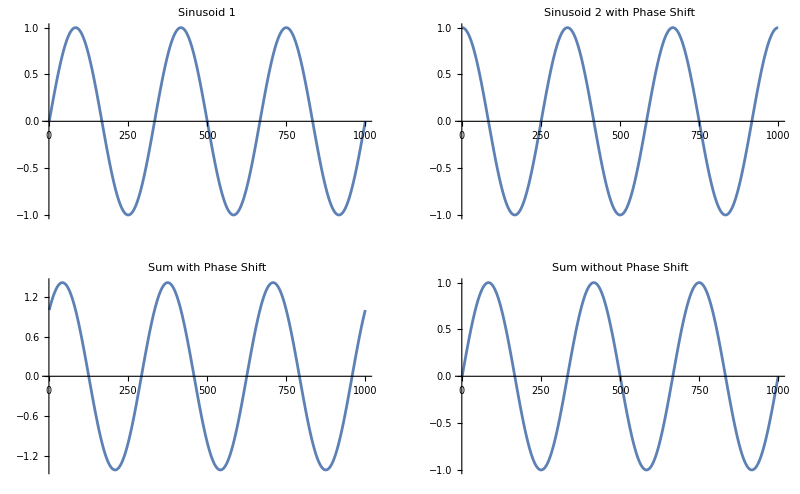

```mathematica
(*Define the parameters*)T=2.*Pi;  (*period for the sine wave*)
n=1000;   (*number of points*)
span=3*T; (*span of the time domain signal*)

(*Two sinusoids with the same frequency and amplitude but different phase*)
sinusoid1=Table[Sin[t],{t,Subdivide[0,span,n-1]}];
sinusoid2=Table[Sin[t+Pi/2],{t,Subdivide[0,span,n-1]}]; (*90-degree phase shift*)

(*Add the sinusoids together*)
combined1=sinusoid1+sinusoid2;
combined2=sinusoid1;

(*Plot the results*)
GraphicsGrid[{{ListPlot[sinusoid1,Joined->True,PlotLabel->"Sinusoid 1",ImageSize->Medium],ListPlot[sinusoid2,Joined->True,PlotLabel->"Sinusoid 2 with Phase Shift",ImageSize->Medium]},{ListPlot[combined1,Joined->True,PlotLabel->"Sum with Phase Shift",ImageSize->Medium],ListPlot[combined2,Joined->True,PlotLabel->"Sum without Phase Shift",ImageSize->Medium]}}]
```

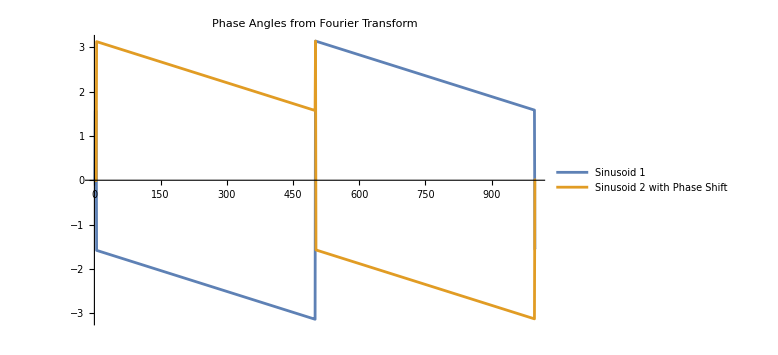

```mathematica
ClearAll["Global`*"];
T=2.*Pi;  (*period for the sine wave*)
n=1000;   (*number of points*)
span=3*T; (*span of the time domain signal*)

(*Two sinusoids with the same frequency and amplitude but different phase*)
sinusoid1=Table[Sin[t],{t,Subdivide[0,span,n-1]}];
sinusoid2=Table[Sin[t+Pi/2],{t,Subdivide[0,span,n-1]}]; (*90-degree phase shift*)

(*Compute the Fourier transform of each sinusoid*)
fft1=Fourier[sinusoid1,FourierParameters->{-1,1}];
fft2=Fourier[sinusoid2,FourierParameters->{-1,1}];

(*Calculate the phase angles*)
phase1=Arg[fft1];
phase2=Arg[fft2];

(*Plot the phase angles*)
ListLinePlot[{phase1,phase2},PlotRange->All,PlotLegends->{"Sinusoid 1","Sinusoid 2 with Phase Shift"},ImageSize->Large,PlotLabel->"Phase Angles from Fourier Transform"]
```